```mathematica
P[n_,k_,j_]:=1/k-P[n/j,k+1,Floor[n/j]]+P[n,k,j-1]
P[n_,k_,1]:=0
```

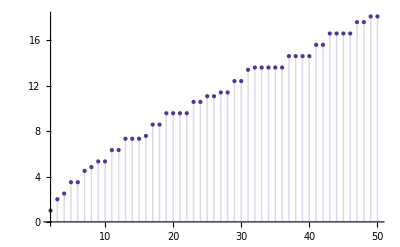

```mathematica
DiscretePlot[P[n,1,n],{n,2,50}]
```

```mathematica
N[P[10,1,10]]
```

5.33333

```mathematica
PPP[n_] := FullSimplify[MangoldtLambda[n]/Log[n]]
```

```mathematica
PPP[8]
```

1/3

```mathematica
Q[n_,k_,j_]:=PPP[j](1/(k!)+Q[n/j,k+1,Floor[n/j]])+Q[n,k,j-1]
Q[n_,k_,1]:=0
```

```mathematica
Q[110,1,110]
```

109

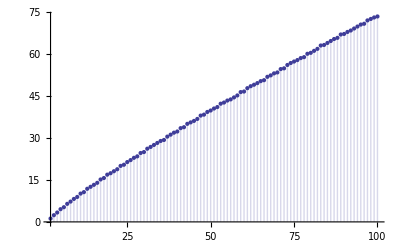

```mathematica
DiscretePlot[ Re[Q[n,1-I,n]],{n,2,100}]
```

```mathematica
Simplify[Q[101, k,101]-Q[100,k,100]]
```

1/(k!)

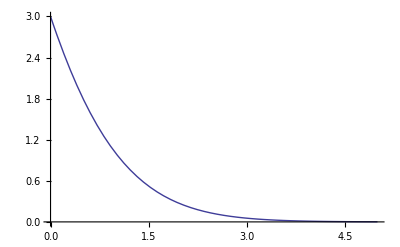

```mathematica
Plot[ 1/(2 (1+k)!)+3/((2+k)!)+6/((3+k)!), {k,0,5}]
```

```mathematica
Simplify[Q[101,k,101]-Q[101,k+1,101]]
```

1/360 (10632/(k!)+21946/((1+k)!)+12107/((2+k)!)-8025/((3+k)!)-24600/((4+k)!)-9540/((5+k)!)-2520/((6+k)!))